# Aristotle's Wheel Paradox

### Author

Eric W. Weisstein
June 25, 2012

This notebook downloaded from http://mathworld.wolfram.com/notebooks/RecreationalMath/AristotlesWheelParadox.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/AristotlesWheelParadox.html.

©2012 Wolfram Research, Inc. except for portions noted otherwise

### Additional Authors

Animation by
Javier H. Ospina H.  
December 9, 2004

## Graphic

Animation by Javier H. Ospina H. (December 9, 2004)

#### V5

```mathematica
movie=With[{rsmall=0.8,rbig=1.6},
Table[Show[Graphics[{
{
GrayLevel[0.5],
Circle[{0,0},rsmall,{-Pi/2,3Pi/2}],
Circle[{2 Pi,0},rsmall,{-Pi/2,3Pi/2}],
Circle[{0,0},rbig,{-Pi/2,3Pi/2}],
Circle[{2 Pi,0},rbig,{-Pi/2,3Pi/2}],
Line[{{0,-rbig},{2 Pi,-rbig}}],
Line[{{0,-rsmall},{2 Pi,-rsmall}}],
Line[{{0,0},{0,-rbig}}],
Line[{{2Pi,0},{2Pi,-rbig}}]
},
{
Blue,
Circle[{t,0},rbig,{3Pi/2-t,3Pi/2}],
Circle[{t,0},rsmall,{3Pi/2-t,3Pi/2}]
},
{Red,Thickness[0.007],
Circle[{t,0},rbig,{-Pi/2,3Pi/2-t}],
Circle[{t,0},rsmall,{-Pi/2,3Pi/2-t}],
Line[{{0,-rbig},{t,-rbig}}],
Line[{{0,-rsmall},{t,-rsmall}}]
},
{Purple,
Line[{{t,0},{rbig Cos[-t-Pi/2]+t,rbig Sin[-t-Pi/2]}}]
}
},
PlotRange->{{-rbig-0.1,2 Pi rbig-rbig},{-rbig-0.5,rbig+0.5}},AspectRatio->Automatic
]],{t,0, 2 Pi,Pi/24}]
];
```

```mathematica
<<Utilities`GIF`;
```

```mathematica
Export[gifs<>"AristotlesWheel.gif",movie]//Timing
```

{2.06575 Second,/troves/MathOzTeX/gifs/AristotlesWheel.gif}

#### V6

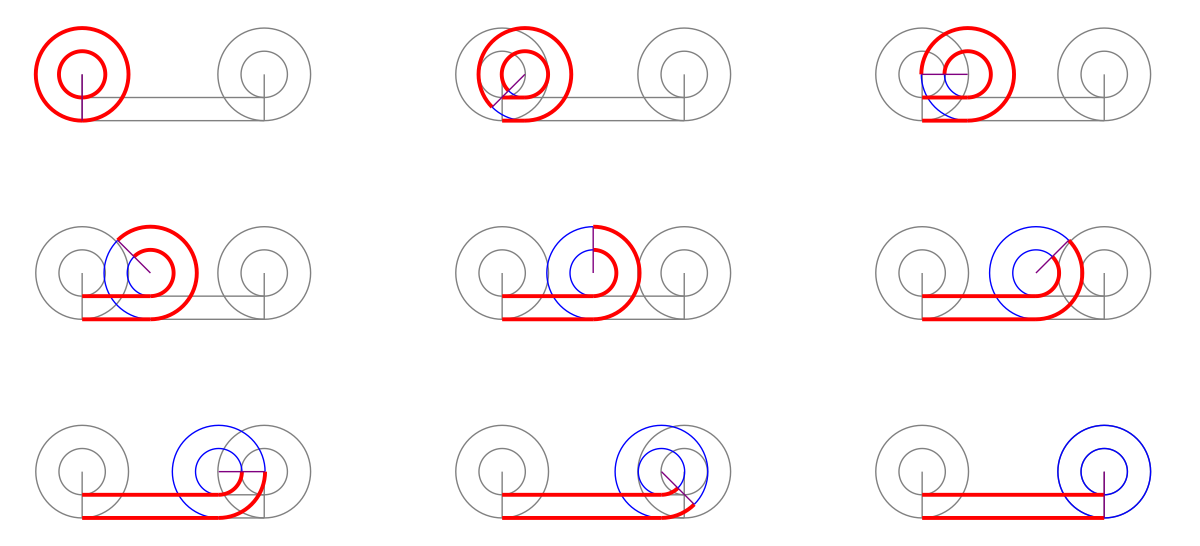

```mathematica
GraphicsGrid[Partition[movie[[1;;49;;6]],3],Spacings->{60,50}]
```